```mathematica
SetDirectory[NotebookDirectory[]];
sinogramdata=Import["sinogram.dat"];
```

```mathematica
sinogramfunc=Interpolation[sinogramdata]
```

InterpolatingFunction[…]

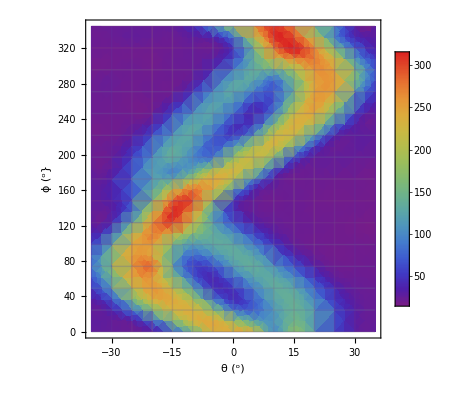

```mathematica
DensityPlot[sinogramfunc[y,x],{y,-35,35},{x,0,345},ColorFunction->"Rainbow",PlotLegends->Automatic,Mesh->Full,FrameLabel->{"θ (^o)", "ϕ (^o}"}]
```

```mathematica
Export["sinogramBet.png",%]
```

sinogram.png

```mathematica
SetDirectory[NotebookDirectory[]];
reconstructdata=Import["sinogrambet.dat"];
```

```mathematica
reconstructdata[[All,{2}]]=-reconstructdata[[All,{2}]];
reconstructfunc=Interpolation[reconstructdata];
```

```mathematica
Export["reconstructBet.dat",reconstructdata]
```

reconstructBet.dat

```mathematica
FindMaximum[reconstructfunc[x,y],{{x,0},{y,24}}]
```

{61.028,{x→0.439145,y→21.5428}}

```mathematica
FindMaximum[reconstructfunc[x,y],{{x,18},{y,0}}]
```

{31.69,{x→15.9331,y→-0.257256}}

```mathematica
NIntegrate[x reconstructfunc[x,y],{x,0.18791870003296407-5.97841353737462*2.53,0.18791870003296407+5.97841353737462*2.53},{y,23.276487200697556-6.592516389292497*2.53,23.530159978908518+6.381623845672643*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,0.18791870003296407-5.97841353737462*2.53,0.18791870003296407+5.97841353737462*2.53},{y,23.276487200697556-6.592516389292497*2.53,23.530159978908518+6.381623845672643*2.53}]
```

0.222448

```mathematica
NIntegrate[x^2 reconstructfunc[x,y],{x,0.18791870003296407-5.97841353737462*2.53,0.18791870003296407+5.97841353737462*2.53},{y,23.276487200697556-6.592516389292497*2.53,23.530159978908518+6.381623845672643*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,0.18791870003296407-5.97841353737462*2.53,0.18791870003296407+5.97841353737462*2.53},{y,23.276487200697556-6.592516389292497*2.53,23.530159978908518+6.381623845672643*2.53}]
```

45.0712

```mathematica
Sqrt[25.77674186168619-0.18791870003296407^2]
```

5.0736

```mathematica
NIntegrate[y reconstructfunc[x,y],{x,0.34695086961-5.055327995904766*2.53,0.34695086961+5.055327995904766*2.53},{y,23.530159978908518-6.381623845672643*2.53,23.530159978908518+6.381623845672643*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,0.34695086961-5.055327995904766*2.53,0.34695086961+5.055327995904766*2.53},{y,23.530159978908518-6.381623845672643*2.53,23.530159978908518+6.381623845672643*2.53}]
```

23.2765

```mathematica
NIntegrate[y^2 reconstructfunc[x,y],{x,0.34695086961-5.055327995904766*2.53,0.34695086961+5.055327995904766*2.53},{y,23.530159978908518-6.381623845672643*2.53,23.530159978908518+6.381623845672643*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,0.34695086961-5.055327995904766*2.53,0.34695086961+5.055327995904766*2.53},{y,23.530159978908518-6.381623845672643*2.53,23.530159978908518+6.381623845672643*2.53}]
```

585.256

```mathematica
Sqrt[585.2561287473274-23.276487200697556^2]
```

6.59252

```mathematica
NIntegrate[x reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.20845136917808738 -4.989890232871057*2.53,-0.20845136917808738 +4.989890232871057*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.20845136917808738-4.989890232871057*2.53,-0.20845136917808738 +4.989890232871057*2.53}]
```

16.5325

```mathematica
NIntegrate[x ^2reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.3828920590650553 -4.989890232871057*2.53,-0.3828920590650553 +4.989890232871057*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.3828920590650553 -4.989890232871057*2.53,-0.3828920590650553 +4.989890232871057*2.53}]
```

310.857

```mathematica
Sqrt[310.85690976169093-16.455921352646207^2]
```

6.32926

```mathematica
NIntegrate[y reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.3828920590650553 -4.989890232871057*2.53,-0.3828920590650553 +4.989890232871057*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.3828920590650553 -4.989890232871057*2.53,-0.3828920590650553 +4.989890232871057*2.53}]
```

-0.208451

```mathematica
NIntegrate[y^2 reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.3828920590650553 -4.989890232871057*2.53,-0.3828920590650553 +4.989890232871057*2.53}]/NIntegrate[ reconstructfunc[x,y],{x,16.455921352646207-5.011429734552087*2.53,16.455921352646207+5.011429734552087*2.53},{y,-0.3828920590650553 -4.989890232871057*2.53,-0.3828920590650553 +4.989890232871057*2.53}]
```

35.5279

```mathematica
Sqrt[25.045610864997048-0.3828920590650553^2]
```

4.98989

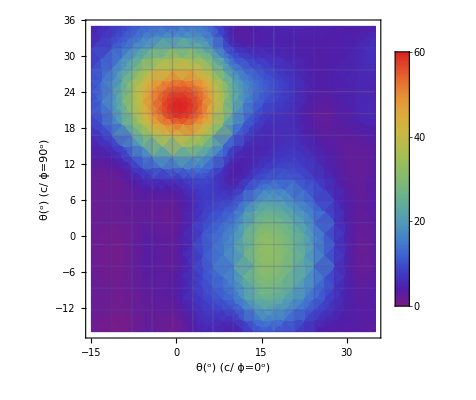

```mathematica
DensityPlot[reconstructfunc[x,y],{x,-15,35},{y,-16,35},ColorFunction->"Rainbow",PlotLegends->Automatic,Mesh->Full,FrameLabel->{"θ(^o) (c/ ϕ=0^o) ", "θ(^o) (c/ ϕ=90^o)"}]
```

```mathematica
Export["ReconstructionBet.png",%]
```

ReconstructionBet.png

```mathematica
ArcTan[21.54277581050957*Pi/180]*15.6*0.3937
```

2.20881

```mathematica
ArcTan[15.933068852355394*Pi/180]*15.6*0.3937
```

1.66583

```mathematica
ConvertX[x_,y_]:=D  (Sin[x](1+Cos [y])+Sin[x]*Sin[y])/((1+Cos[x])(1+Cos[y])+Sin[x]*Sin[y])
```

```mathematica
ConvertYWeak[x_,y_]:=(1+Cos[x])/Sin[x]*ConvertX[x,y]-D;
```

```mathematica
ConvertYStrong[x_,y_]:=-((1+Cos[y])/Sin[y])^-1*(ConvertX[x,y]-D);
```

```mathematica
(*Fonte Forte*)
```

```mathematica
ConvertX[0.18791870003296407*Pi/180,23.530159978908518*Pi/180]/.D->16.9*0.393701
```

0.0131792

```mathematica
ConvertYWeak[0.18791870003296407*Pi/180,23.530159978908518*Pi/180]/.D->16.9*0.393701
```

1.38302

```mathematica
ConvertYWeak[5.0736011297562715*Pi/180,6.092516389292497*Pi/180]/.D->16.9*0.393701
```

0.337601

```mathematica
ConvertX[5.0736011297562715*Pi/180,6.092516389292497*Pi/180]/.D->16.9*0.393701
```

0.309739

```mathematica
(*Fonte Fraca*)
```

```mathematica
ConvertX[16.53251033971853*Pi/180,-0.20845136917808738*Pi/180]/.D->16.9*0.3937
```

0.96514

```mathematica
ConvertYWeak[16.53251033971853*Pi/180,-0.20845136917808738*Pi/180]/.D->16.9*0.3937
```

-0.0103477

```mathematica
ConvertX[5.011429734552087*Pi/180,4.989890232871057*Pi/180]/.D->16.9*0.3937
```

0.303273

```mathematica
ConvertYWeak[5.011429734552087*Pi/180,4.989890232871057*Pi/180]/.D->16.9*0.3937
```

0.276697

```mathematica
(1.383-1.5)/0.338
```

-0.346154

```mathematica
$\
```